Clear::ssym: q1 ， q2 ， q3 is not a symbol or a string.

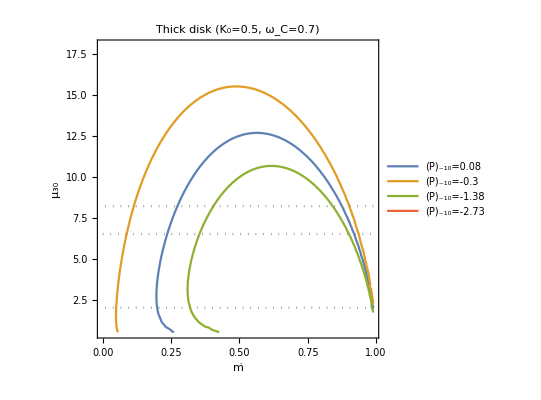

```mathematica
(*
Thick disk model/Reference model
Subscript[K, 0]=0.5,Subscript[ω, C]=0.7
N/(Subscript[N, 0]')=f(Subscript[ω, s]')
(-4/5 πMR^2 P^2 Ṗ)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)u^(2/7)A^(-1/7)(Ṁ)^(6/7))=1-1/Subscript[Aω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1(Ṁ)^(-3/7)μ^(6/7)
*)
Clear[w,k,G,M,R,P,u,MEdd,a,b,q1，q2，q3,q4,x,A,fig1,equ]
w=0.7;
k=0.5;
G=6.67*10^-8;
M=2.8*10^33;
(*M=1.4 M_⊙*)
R=10^6;
P=1.37;
qdot101=-1.2;
qdot102=-0.3;
qdot103=-1.87;
qdot104=-2.73;
(*q=Subscript[Ṗ, -10]={0.08,-0.3,-1.38,-2.73}*)
MEdd=10^20;
a=1/w*k^(3/2)*(G*M)^(-5/7)*P^-1*(MEdd)^(-3/7)*2.80517*10^26;
(*a=1/Subscript[ω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1 Subscript[Ṁ, E]^(-3/7)
=1/Subscript[ω, C]*2^(11/14)Subscript[πK, 0]^(3/2)(GM)^(-5/7)P^-1 Subscript[Ṁ, E]^(-3/7)*(10^30)^(6/7)
2.^(11/14)*Pi*(10^30)^(6/7)=2.80517*10^26*)
b=(M*R^2*P^2)/(k^(1/2)*(G*M)^(3/7)*(MEdd)^(6/7))*(-7.08457*10^-19);
(*b=(-4/5 πMR^2 P^2)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)Subscript[Ṁ, E]^(6/7))
=(-4/5 πMR^2 P^2*10^-10)/(2^(-1/14)Subscript[K, 0]^(1/2)(GM)^(3/7)Subscript[Ṁ, E]^(6/7)*(10^30)^(2/7))
(-4/5*Pi*10^-10)/(2.^(-1/14)*(10^30)^(2/7))=-7.08457*10^-19*)
equ=(1-x)^(-1/14)x^(6/7)u^(2/7)-a(1-x)^(-4/7)x^(3/7)u^(8/7);
b*q1;
b*q2;
b*q3;
b*q4;
(*
x=ṁ
Ṗ 和 ṁ 的关系
(b Subscript[Ṗ, -10])/(A^(-1/7)(ṁ)^(6/7)Subscript[μ, 30]^(2/7))=1-a(ṁ)^(-3/7)Subscript[μ, 30]^(6/7)
Subscript[Ṗ, -10]=(((ṁ)^(3/7)-a)(ṁ)^(3/7))/(b(1-ṁ)^(4/7)) (*A=(1-ṁ)^(1/2)*)
*)
fig1=ContourPlot[
{(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q1==0,
(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q2==0,
(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q3==0,
(1-x)^(-1/14)*x^(6/7)*u^(2/7)-a*(1-x)^(-4/7)*x^(3/7)*u^(8/7)-b*q4==0},
{x,0,0.99},{u,0.5,18},
PlotLabel->"Thick disk (K_0=0.5, ω_C=0.7)",
PlotLegends->{"(Ṗ)_-10=0.08","(Ṗ)_-10=-0.3","(Ṗ)_-10=-1.38","(Ṗ)_-10=-2.73"},
FrameLabel->{"ṁ","μ_30"},
ContourStyle->{,,,,{Gray,Dotted},{Gray,Dotted},{Gray,Dotted}}]
```

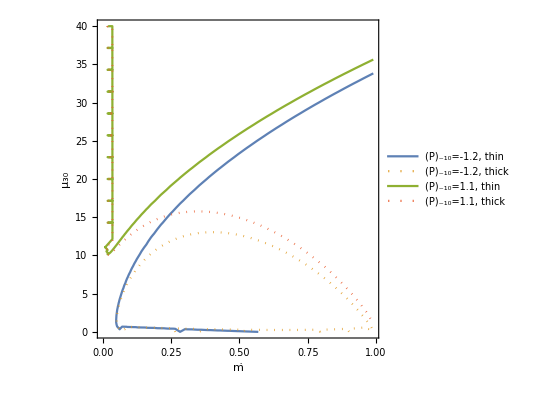

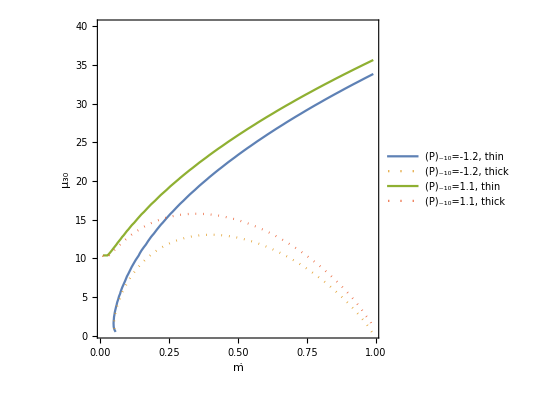

```mathematica
Clear["`*"]
G=6.67*10^-8;
M=2.8*10^33;
(*M=1.4 M_⊙*)
R=10^6;
Irot=10^45;
Mdotcr=10^20;

P=1.37;
omegac=0.7;
xi=0.5;
pdot101=-1.2;
pdot102=-0.3;
pdot103=-1.87;
pdot104=-2.73;
pdot105=1.1;

aconst=1.77*10^-18*xi^(-1/2)*Irot*(G*M)^(-3/7)*Mdotcr^(-6/7);
bconst=2.8*10^26*xi^(3/2)*(G*M)^(-5/7)*Mdotcr^(-3/7)*omegac^-1;

(*mdot=Mdot/Mdotcr;*)
A=√(1-mdot);

equthin=1-(bconst*mu30^(6/7))/(P*mdot^(3/7))+(aconst*pdot)/(mu30^(2/7)*P^2*mdot^(6/7));
equthick=1-(bconst*mu30^(6/7))/(A^(10/7)*P*mdot^(3/7))+(aconst*pdot)/(A^(6/7)*mu30^(2/7)*P^2*mdot^(6/7));
equthin1=equthin/.pdot->pdot101;
equthick1=equthick/.pdot->pdot101;
equthin5=equthin/.pdot->pdot105;
equthick5=equthick/.pdot->pdot105;
ContourPlot[{equthin1==0,equthick1==0,equthin5==0,equthick5==0},{mdot,0,0.99},{mu30,0.,40},
PlotLegends->{"(Ṗ)_-10=-1.2, thin","(Ṗ)_-10=-1.2, thick","(Ṗ)_-10=1.1, thin","(Ṗ)_-10=1.1, thick"},
FrameLabel->{"ṁ","μ_30"},
ContourStyle->{,{,Dotted},,{,Dotted}}]
ContourPlot[{equthin1==0,equthick1==0,equthin5==0,equthick5==0},{mdot,0.01,0.99},{mu30,0.5,40},
PlotLegends->{"(Ṗ)_-10=-1.2, thin","(Ṗ)_-10=-1.2, thick","(Ṗ)_-10=1.1, thin","(Ṗ)_-10=1.1, thick"},
FrameLabel->{"ṁ","μ_30"},
ContourStyle->{,{,Dotted},,{,Dotted}}]
```

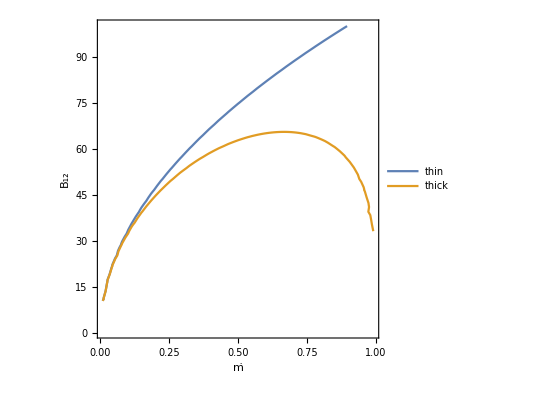

```mathematica
Clear["`*"]
G=6.67*10^-8;
M=2.8*10^33;
(*M=1.4 M_⊙*)
R=10^6;
Irot=10^45;
Mdotcr=10^20;

P=1.37;
omegac=0.7;
xi=0.5;
Omegas=2*Pi/P;

Mdot=mdot*Mdotcr;
A=√(1-mdot);
mu=mu30*10^30;
mu30=0.5*B12;

Rinthin=xi*(mu^4/(2*G*M*Mdot^2))^(1/7);
Rinthick=A^(-2/7)*Rinthin;
Rco=((G*M)/Omegas^2)^(1/3);
eqthin=Rinthin-Rco;
eqthick=Rinthick-Rco;

ContourPlot[{eqthin==0,eqthick==0},{mdot,0.01,0.99},{B12,0.5,100},
PlotLegends->{"thin","thick"},
FrameLabel->{"ṁ","B_12"}]
```

```mathematica
NSolve[eqthin/.B12->10]
```

{{mdot→8.94854×10^57},{mdot→-8.94854×10^57}}